```mathematica
With[{max=20},ListPlot3D[Flatten[Monitor[Table[Table[{n,k,N[Log[ChromaticPolynomial[JacobsThalGraph[n],k]]]},{n,1,max}],{k,1,max}],{n,k}],1], ColorFunction->"Rainbow"]
]
```

-Graphics3D-

```mathematica
ListPlot[%]
```

-Graphics-

```mathematica
With[{max=8},Flatten[Monitor[Table[Table[{n,k,N[Log[ChromaticPolynomial[JacobsThalGraph[n],k]+1]]},{n,1,max}],{k,1,max}],{n,k}],1]
]
```

{{1,1,0.},{2,1,0.},{3,1,0.},{4,1,0.},{5,1,0.},{6,1,0.},{7,1,0.},{8,1,0.},{1,2,0.},{2,2,0.},{3,2,0.},{4,2,0.},{5,2,0.},{6,2,0.},{7,2,0.},{8,2,0.},{1,3,0.},{2,3,1.94591},{3,3,0.},{4,3,1.94591},{5,3,0.},{6,3,1.94591},{7,3,0.},{8,3,1.94591},{1,4,3.21888},{2,4,4.57471},{3,4,4.79579},{4,4,5.66643},{5,4,6.22456},{6,4,6.96319},{7,4,7.6212},{8,4,8.32579},{1,5,5.4848},{2,5,6.66058},{3,5,7.4961},{4,5,8.51339},{5,5,9.50607},{6,5,10.5448},{7,5,11.5954},{8,5,12.6628},{1,6,6.98564},{2,6,8.3141},{3,6,9.4971},{4,6,10.7485},{5,6,12.0064},{6,6,13.2882},{7,6,14.5871},{8,6,15.9028},{1,7,8.11999},{2,7,9.63763},{3,7,11.0772},{4,7,12.5483},{5,7,14.0264},{6,7,15.5179},{7,7,17.0216},{8,7,18.5376},{1,8,9.03611},{2,8,10.7298},{3,8,12.3753},{4,8,14.0375},{5,8,15.7047},{6,8,17.3797},{7,8,19.0625},{8,8,20.7534}}

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph[n],x],{n,1,20}]
```

{18 x-39 x^2+29 x^3-9 x^4+x^5,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6,210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7,-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9,-6304 x+23030 x^2-36115 x^3+32228 x^4-18158 x^5+6734 x^6-1652 x^7+260 x^8-24 x^9+x^10,19170 x-76425 x^2+133172 x^3-134592 x^4+87822 x^5-38808 x^6+11802 x^7-2448 x^8+333 x^9-27 x^10+x^11,-58024 x+250756 x^2-480554 x^3+542325 x^4-402090 x^5+206262 x^6-74886 x^7+19290 x^8-3465 x^9+415 x^10-30 x^11+x^12,175098 x-815419 x^2+1703943 x^3-2122890 x^4+1762035 x^5-1028940 x^6+434280 x^7-133716 x^8+29865 x^9-4730 x^10+506 x^11-33 x^12+x^13,-527344 x+2632626 x^2-5955413 x^3+8114854 x^4-7451235 x^5+4878423 x^6-2346564 x^7+840708 x^8-224631 x^9+44275 x^10-6270 x^11+606 x^12-36 x^13+x^14,1586130 x-8449805 x^2+20566454 x^3-30412616 x^4+30595279 x^5-22187880 x^6+11977251 x^7-4894032 x^8+1522521 x^9-359216 x^10+63349 x^11-8112 x^12+715 x^13-39 x^14+x^15,-4766584 x+26988800 x^2-70308916 x^3+112097167 x^4-122564533 x^5+97488391 x^6-58339281 x^7+26769171 x^8-9502779 x^9+2611609 x^10-551551 x^11+87997 x^12-10283 x^13+833 x^14-42 x^15+x^16,14316138 x-85847679 x^2+238288289 x^3-407345890 x^4+480815790 x^5-416054730 x^6+273275002 x^7-139086090 x^8+55469700 x^9-17401670 x^10+4282278 x^11-818454 x^12+119210 x^13-12810 x^14+960 x^15-45 x^16+x^17,-42981184 x+272104942 x^2-801572711 x^3+1462189640 x^4-1852588780 x^5+1732055052 x^6-1238442296 x^7+692180632 x^8-306318870 x^9+107995030 x^10-30344600 x^11+6759480 x^12-1179724 x^13+158060 x^14-15720 x^15+1096 x^16-48 x^17+x^18,129009090 x-859820305 x^2+2678789160 x^3-5192729152 x^4+7027410700 x^5-7057699600 x^6+5455582132 x^7-3320841472 x^8+1614431962 x^9-631768280 x^10+199541342 x^11-50762816 x^12+10327772 x^13-1658384 x^14+205700 x^15-19040 x^16+1241 x^17-51 x^18+x^19,-387158344 x+2709584124 x^2-8900644238 x^3+18268117737 x^4-26294458212 x^5+28225855548 x^6-23449792044 x^7+15438021300 x^8-8176584078 x^9+3515960162 x^10-1232881650 x^11+352621854 x^12-81944148 x^13+15341004 x^14-2280924 x^15+263364 x^16-22797 x^17+1395 x^18-54 x^19+x^20,1161737178 x-8518270019 x^2+29421543851 x^3-63731736138 x^4+97201627413 x^5-111042213912 x^6+98651269824 x^7-69829031496 x^8+40012581726 x^9-18749358004 x^10+7225807160 x^11-2294820684 x^12+599642394 x^13-128241336 x^14+22232736 x^15-3077544 x^16+332367 x^17-27018 x^18+1558 x^19-57 x^20+x^21,-3485735824 x+26721527978 x^2-96805314889 x^3+220680256650 x^4-355463627145 x^5+430518782301 x^6-407218288728 x^7+308344753560 x^8-190021568610 x^9+96355250810 x^10-40474077020 x^11+14129618204 x^12-4100197530 x^13+986102850 x^14-195311640 x^15+31527384 x^16-4082397 x^17+414105 x^18-31730 x^19+1730 x^20-60 x^21+x^22,10458256050 x-83660805525 x^2+317187280010 x^3-758995506920 x^4+1287388660005 x^5-1647528009120 x^6+1652808692325 x^7-1332887593248 x^8+878925432510 x^9-479431303120 x^10+217966672014 x^11-82948927152 x^12+26462459114 x^13-7068428640 x^14+1574518410 x^15-290389920 x^16+43852095 x^17-5333832 x^18+510055 x^19-36960 x^20+1911 x^21-63 x^22+x^23,-31376865304 x+261462692728 x^2-1035332746040 x^3+2594522452291 x^4-4621945952855 x^5+6231306279429 x^6-6607732208847 x^7+5653376603589 x^8-3971330880858 x^9+2318423279150 x^10-1134053681530 x^11+467174634654 x^12-162486796654 x^13+47719838474 x^14-11806867710 x^15+2449161066 x^16-422597373 x^17+59949351 x^18-6874637 x^19+621775 x^20-42735 x^21+2101 x^22-66 x^23+x^24}

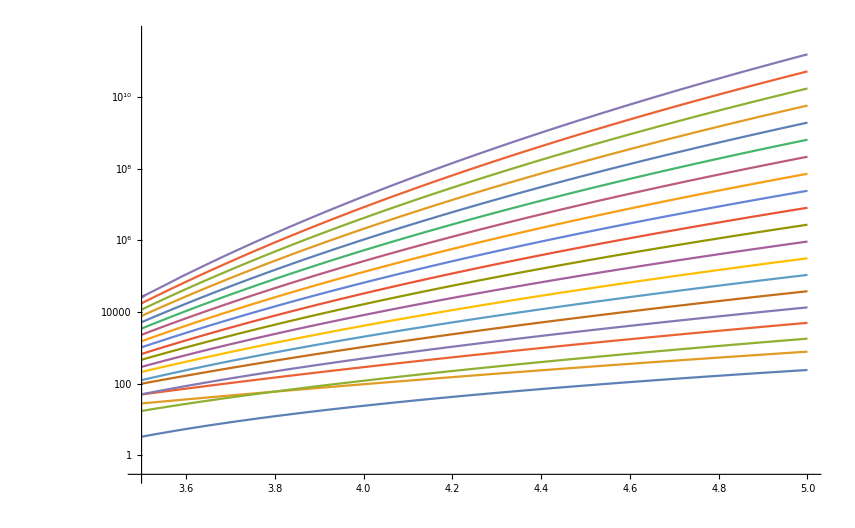

```mathematica
LogPlot[{18 x-39 x^2+29 x^3-9 x^4+x^5,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6,210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7,-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9,-6304 x+23030 x^2-36115 x^3+32228 x^4-18158 x^5+6734 x^6-1652 x^7+260 x^8-24 x^9+x^10,19170 x-76425 x^2+133172 x^3-134592 x^4+87822 x^5-38808 x^6+11802 x^7-2448 x^8+333 x^9-27 x^10+x^11,-58024 x+250756 x^2-480554 x^3+542325 x^4-402090 x^5+206262 x^6-74886 x^7+19290 x^8-3465 x^9+415 x^10-30 x^11+x^12,175098 x-815419 x^2+1703943 x^3-2122890 x^4+1762035 x^5-1028940 x^6+434280 x^7-133716 x^8+29865 x^9-4730 x^10+506 x^11-33 x^12+x^13,-527344 x+2632626 x^2-5955413 x^3+8114854 x^4-7451235 x^5+4878423 x^6-2346564 x^7+840708 x^8-224631 x^9+44275 x^10-6270 x^11+606 x^12-36 x^13+x^14,1586130 x-8449805 x^2+20566454 x^3-30412616 x^4+30595279 x^5-22187880 x^6+11977251 x^7-4894032 x^8+1522521 x^9-359216 x^10+63349 x^11-8112 x^12+715 x^13-39 x^14+x^15,-4766584 x+26988800 x^2-70308916 x^3+112097167 x^4-122564533 x^5+97488391 x^6-58339281 x^7+26769171 x^8-9502779 x^9+2611609 x^10-551551 x^11+87997 x^12-10283 x^13+833 x^14-42 x^15+x^16,14316138 x-85847679 x^2+238288289 x^3-407345890 x^4+480815790 x^5-416054730 x^6+273275002 x^7-139086090 x^8+55469700 x^9-17401670 x^10+4282278 x^11-818454 x^12+119210 x^13-12810 x^14+960 x^15-45 x^16+x^17,-42981184 x+272104942 x^2-801572711 x^3+1462189640 x^4-1852588780 x^5+1732055052 x^6-1238442296 x^7+692180632 x^8-306318870 x^9+107995030 x^10-30344600 x^11+6759480 x^12-1179724 x^13+158060 x^14-15720 x^15+1096 x^16-48 x^17+x^18,129009090 x-859820305 x^2+2678789160 x^3-5192729152 x^4+7027410700 x^5-7057699600 x^6+5455582132 x^7-3320841472 x^8+1614431962 x^9-631768280 x^10+199541342 x^11-50762816 x^12+10327772 x^13-1658384 x^14+205700 x^15-19040 x^16+1241 x^17-51 x^18+x^19,-387158344 x+2709584124 x^2-8900644238 x^3+18268117737 x^4-26294458212 x^5+28225855548 x^6-23449792044 x^7+15438021300 x^8-8176584078 x^9+3515960162 x^10-1232881650 x^11+352621854 x^12-81944148 x^13+15341004 x^14-2280924 x^15+263364 x^16-22797 x^17+1395 x^18-54 x^19+x^20,1161737178 x-8518270019 x^2+29421543851 x^3-63731736138 x^4+97201627413 x^5-111042213912 x^6+98651269824 x^7-69829031496 x^8+40012581726 x^9-18749358004 x^10+7225807160 x^11-2294820684 x^12+599642394 x^13-128241336 x^14+22232736 x^15-3077544 x^16+332367 x^17-27018 x^18+1558 x^19-57 x^20+x^21,-3485735824 x+26721527978 x^2-96805314889 x^3+220680256650 x^4-355463627145 x^5+430518782301 x^6-407218288728 x^7+308344753560 x^8-190021568610 x^9+96355250810 x^10-40474077020 x^11+14129618204 x^12-4100197530 x^13+986102850 x^14-195311640 x^15+31527384 x^16-4082397 x^17+414105 x^18-31730 x^19+1730 x^20-60 x^21+x^22,10458256050 x-83660805525 x^2+317187280010 x^3-758995506920 x^4+1287388660005 x^5-1647528009120 x^6+1652808692325 x^7-1332887593248 x^8+878925432510 x^9-479431303120 x^10+217966672014 x^11-82948927152 x^12+26462459114 x^13-7068428640 x^14+1574518410 x^15-290389920 x^16+43852095 x^17-5333832 x^18+510055 x^19-36960 x^20+1911 x^21-63 x^22+x^23,-31376865304 x+261462692728 x^2-1035332746040 x^3+2594522452291 x^4-4621945952855 x^5+6231306279429 x^6-6607732208847 x^7+5653376603589 x^8-3971330880858 x^9+2318423279150 x^10-1134053681530 x^11+467174634654 x^12-162486796654 x^13+47719838474 x^14-11806867710 x^15+2449161066 x^16-422597373 x^17+59949351 x^18-6874637 x^19+621775 x^20-42735 x^21+2101 x^22-66 x^23+x^24},{x,3.5,5}]
```

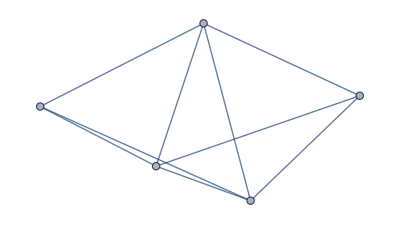
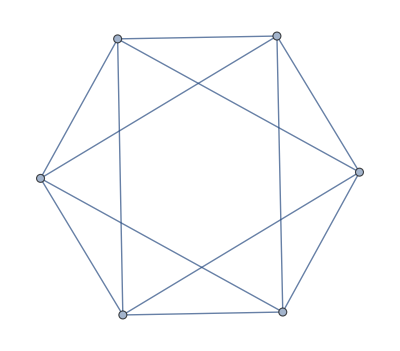
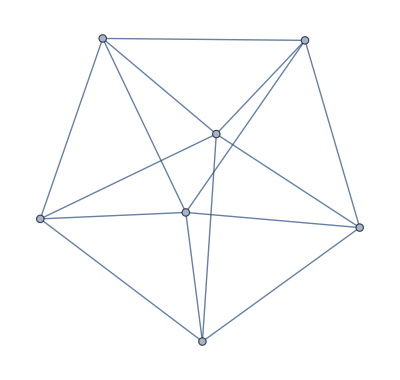
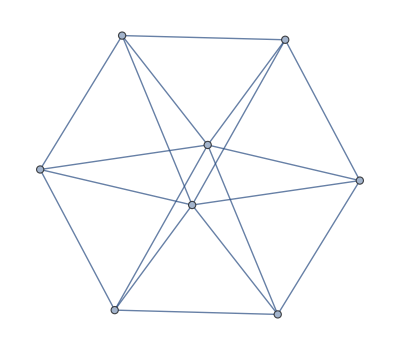
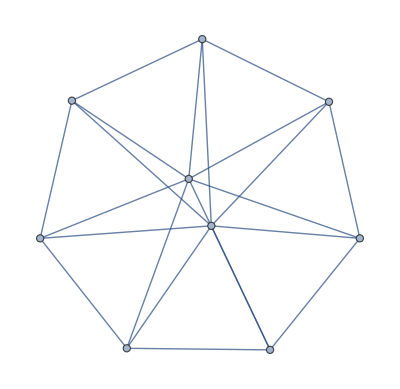
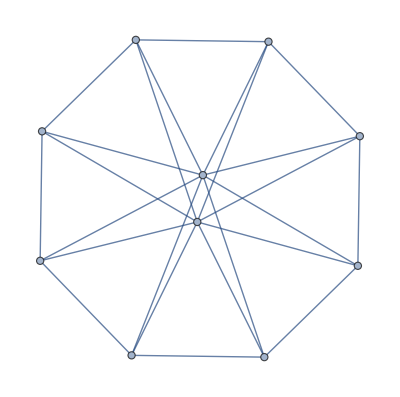
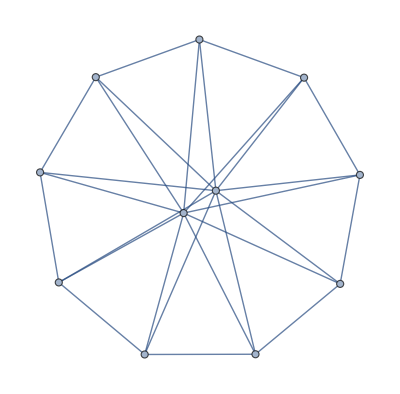
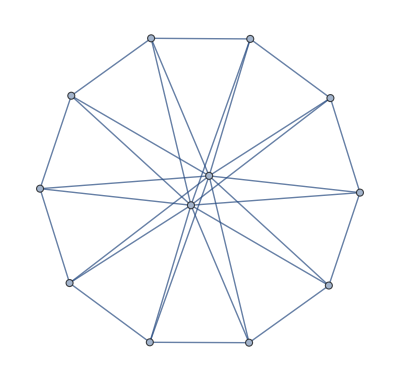

```mathematica
Table[JacobsThalGraph[n],{n,1,10}]
```

```mathematica
6!/(6-3)!
```

120

```mathematica
MatrixForm[With[
{max=12},
Monitor[Table[Table[With[{g=JacobsThalGraph[n]},
ChromaticPolynomial[g,k]/(k!/(k-3)!)],{n,1,max}],{k,4,max}],{n,k}]
]]
```

(1 | 4 | 5 | 12 | 21 | 44 | 85 | 172 | 341 | 684 | 1365 | 2732
4 | 13 | 30 | 83 | 224 | 633 | 1810 | 5263 | 15444 | 45653 | 135590 | 404043
9 | 34 | 111 | 388 | 1365 | 4918 | 18027 | 67192 | 254001 | 971722 | 3754023 | 14617516
16 | 73 | 308 | 1341 | 5880 | 26129 | 117532 | 535237 | 2466464 | 11493465 | 54111876 | 257137613
25 | 136 | 705 | 3716 | 19685 | 105096 | 565465 | 3067276 | 16776045 | 92518256 | 514419425 | 2883066036
36 | 229 | 1410 | 8767 | 54696 | 342889 | 2160270 | 13682227 | 87137556 | 558134749 | 3595974330 | 23306006887
49 | 358 | 2555 | 18348 | 132069 | 953618 | 6908335 | 50222488 | 366470489 | 2684598078 | 19746623715 | 145861863428
64 | 529 | 4296 | 35033 | 286160 | 2342433 | 19217752 | 158046697 | 1303115616 | 10773603377 | 89326932968 | 742858417401
81 | 748 | 6813 | 62236 | 569205 | 5213764 | 47832957 | 439587532 | 4047196869 | 37333862740 | 345095673741 | 3196770154588)